{structure}

{0,0,1,1}

{3.07221,2.93407,2.45587,2.0428}

{5.033,1.606,0.279,0}

{{0,0,0,0},{0,0,0,0},{0,0,0,16/3},{0,0,0,0}}

{quantity}

xi-Cos[xi] Sin[xi]

√(mi^2+xi^2/R^2)

(√(mi^2+xi^2/R^2) (xi (xi-Cos[xi] Sin[xi])-Sin[xi (xi-Cos[xi] Sin[xi])]^2/(xi (xi-Cos[xi] Sin[xi])))-mi (Cos[xi (xi-Cos[xi] Sin[xi])] Sin[xi (xi-Cos[xi] Sin[xi])]-Sin[xi (xi-Cos[xi] Sin[xi])]^2/(xi (xi-Cos[xi] Sin[xi]))))/(√(mi^2+xi^2/R^2) (xi-Sin[xi]^2/xi)-mi (Cos[xi] Sin[xi]-Sin[xi]^2/xi))

NIntegrate::nlim: r = 0.01 R is not a valid limit of integration.

R NIntegrate[(ρ[mi,xi,r] ρ[mj,xj,r])/r^2,{r,0.01 R,R}]

{interaction energy}

0.296/Log[1+3.55872/R]

NIntegrate::nlim: r = 0.01 R is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-(1.57867 NIntegrate[(ρ[0.279,2.45587,r] ρ[0,2.0428,r])/r^2,{r,0.01 R,R}])/Log[1+3.55872/R]

NIntegrate::nlim: r = 0.01 R is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-2.93333 NIntegrate[(ρ[0.279,2.45587,r] ρ[0,2.0428,r])/r^2,{r,0.01 R,R}]

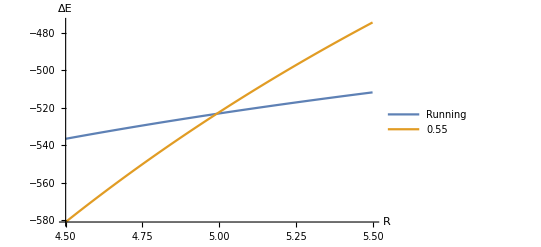

{integrate}

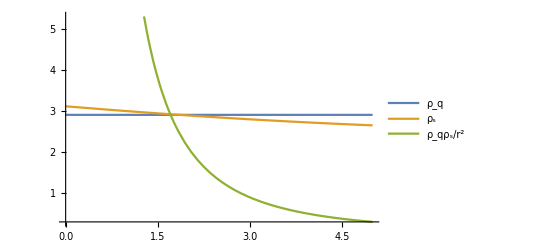

-537.373

-47.2256

```mathematica
{"structure"}
n={0,0,1,1}
x={3.07221,2.93407,2.45587,2.0428}
m={5.033,1.606,0.279,0}
CEI={{0,0,0,0},{0,0,0,0},{0,0,0,16/3},{0,0,0,0}}

{"quantity"}
y[xi_]=xi-Sin[xi]Cos[xi]
ω[mi_,xi_,R_]=(mi^2+xi^2/R^2)^(1/2)
ρ[mi_,xi_,R_]=(ω[mi,xi,R](xi*y[xi]-Sin[xi*y[xi]]^2/(xi*y[xi]))-mi(Sin[xi*y[xi]]Cos[xi*y[xi]]-Sin[xi*y[xi]]^2/(xi*y[xi])))/(ω[mi,xi,R](xi-Sin[xi]^2/xi)-mi(Sin[xi]Cos[xi]-Sin[xi]^2/xi))
f[mi_,xi_,mj_,xj_,R_]=R*NIntegrate[ρ[mi,xi,r]*ρ[mj,xj,r]/r^2,{r,0.01R,R}]

{"interaction energy"}
α[R_]=0.296/Log[1+1/(R*0.281)]
RunningΔEE[R_]=-α[R]/R*Sum[CEI[[p,q]]*f[m[[p]],x[[p]],m[[q]],x[[q]],R],{p,1,4},{q,1,4}]
ΔEE[R_]=-0.55/R*Sum[CEI[[p,q]]*f[m[[p]],x[[p]],m[[q]],x[[q]],R],{p,1,4},{q,1,4}]
Plot[{RunningΔEE[R],ΔEE[R]},{R,4.5,5.5},AxesLabel->{"R","ΔE"},PlotLegends->Placed[{"Running","0.55"},{0.7,0.8}]]

{"integrate"}
Plot[{ρ[0,2.04,R],ρ[0.279,2.45,R],ρ[0,2.04,R]*ρ[0.279,2.45,R]/R^2},{R,0,5},PlotLegends->Placed[{"ρ_q","ρ_s","ρ_qρ_s/r^2"},{0.7,0.8}]]
RunningΔEE[4.47]
-α[4.47]/4.47*Sum[CEI[[p,q]]*4.47*NIntegrate[ρ[0,2.0428,r]*ρ[0.279,2.45587,r]/r^2,{r,0.1*4.47,4.47}],{p,1,4},{q,1,4}]
```